```mathematica
SetDirectory["/media/alexander/9e1069d5-cd39-4e83-8eff-49b4335462dd/home/ns-cclolab/Documents/ALEX_0605-20230605T073644Z-001/ALEX_0605/LIF_Logic/feedforward_mag"]
fileList=FileNames["*"];
Length[fileList]
(*Step 3:Extract the indices and read the files into an Association*)
Monitor[
table=Table[Import["e_"<>IntegerString[e,10,3]<>"_i_"<>IntegerString[i,10,3]<>"_k_"<>IntegerString[k,10,3],"Table"][[2;;-1,1]],{e,0,23},{i,0,23},{k,0,7}];
(*Use the tableList*)
Dimensions[tableList],{e,i,k}]
```

/media/alexander/9e1069d5-cd39-4e83-8eff-49b4335462dd/home/ns-cclolab/Documents/ALEX_0605-20230605T073644Z-001/ALEX_0605/LIF_Logic/feedforward_mag

7744

{16}

```mathematica
{If[data[[2,2,60]]>20,1,0],If[data[[2,2,140]]>20,1,0],If[data[[2,2,220]]>20,1,0]}
```

```mathematica
{1,1,1}
```

{1,1,1}

```mathematica
isGate[data_,thresh_]:=Block[{seg},
seg={If[data[[60]]>thresh,1,0],If[data[[140]]>thresh,1,0],If[data[[220]]>20,1,0],If[data[[300]]>thresh,1,0]};
Piecewise[{
{1,seg=={1,1,1,1}},
{2,seg=={1,1,1,0}},
{3,seg=={0,1,1,0}},
{4,seg=={1,0,0,0}},
{5,seg=={0,1,1,1}},
{6,seg=={1,0,0,1}},
{7,seg=={0,0,0,1}},
{8,seg=={0,0,0,0}}
}]
]
tot =16
dat=Table[isGate[table[[i,j,k]],1],{i,1,tot},{j,1,tot},{k,1,20}]
```

16

Part::partw: Part 220 of {0.,50.,150.,200.,150.,150.,200.,150.,150.,150.,«141»} does not exist.

Part::partw: Part 300 of {0.,50.,150.,200.,150.,150.,200.,150.,150.,150.,«141»} does not exist.

Part::partw: Part 220 of {0.,50.,150.,200.,150.,150.,200.,150.,150.,150.,«141»} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

$Aborted

```mathematica
ListPlot[data[[20,20]]]
```

Part::partw: Part 20 of {«1»} does not exist.

ListPlot::lpn: «1» is not a list of numbers or pairs of numbers.

ListPlot[{{1},{1},{1},{1},{1},{1},{1},{1}}⟦20,20⟧]
 |  |  |  |

0.65

RGBColor[0.8, 0.1, 0.1]

RGBColor[0.9, 0.5, 0.2]

RGBColor[0.9, 0.8, 0.3]

RGBColor[0.1, 0.8, 0.4]

RGBColor[0.1, 0.4, 0.8]

RGBColor[0.7, 0.4, 0.8]

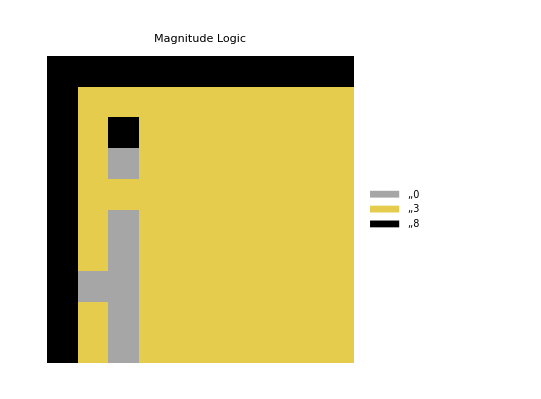

{0.,50.,150.,200.,150.,150.,200.,150.,150.,150.,150.,200.,150.,150.,200.,150.,150.,200.,200.,150.,150.,200.,150.,150.,200.,150.,150.,200.,150.,150.,200.,150.,150.,150.,150.,200.,200.,150.,150.,200.,150.,150.,200.,150.,150.,200.,150.,150.,200.,150.,150.,200.,150.,150.,200.,150.,150.,200.,150.,150.,150.,150.,200.,150.,150.,200.,150.,150.,200.,200.,150.,150.,200.,150.,150.,200.,150.,150.,150.,150.,200.,150.,150.,200.,150.,150.,200.,150.,150.,200.,150.,150.,200.,150.,150.,200.,150.,150.,200.,150.,150.,200.,150.,150.,200.,150.,150.,150.,150.,200.,150.,150.,200.,150.,150.,150.,150.,200.,200.,150.,150.,200.,150.,150.,200.,150.,150.,200.,150.,150.,200.,150.,150.,200.,150.,150.,200.,150.,150.,200.,150.,150.,200.,150.,150.,200.,150.,150.,200.,150.,150.}

```mathematica
grey=.65
red = RGBColor[.8,.1,.1]
orange=  RGBColor[.9,.5,.2]
yellow=RGBColor[.9,.8,.3]
green= RGBColor[.1,.8,.4]
blue =RGBColor[.1,.4,.8]
purple=RGBColor[.7,.4,.8]

ArrayPlot[dat,ColorRules->
{8->Black,1->White,4->red,2->orange,3->yellow,5->green,7->blue,6->purple,0->GrayLevel[grey],"NIMP1"->GrayLevel[grey],"NIMP2"->GrayLevel[grey],"AIMP1"->GrayLevel[grey],"AIMP2"->GrayLevel[grey],"XIMP1"->GrayLevel[grey],"XIMP2"->GrayLevel[grey],"IMP1"->GrayLevel[grey],"IMP2"->GrayLevel[grey]},PlotLegends->Automatic,DataRange->{{1.5,4.5},{-2.5,0.5}},FrameTicks->Automatic,FrameLabel->{"Inhibitory Bias","Excitatory Bias"},PlotLabel->Style["Magnitude Logic","Title",Black,24]]
```

```mathematica
Dimensions[table]
```

{16,16,20,151}

```mathematica
dat=Table[isGate[table[[i,j,k]],1],{i,1,tot},{j,1,tot},{k,1,7}]
```

{{{8,8,8,8,8,8,8},{8,8,8,8,8,8,8},{8,8,8,8,8,8,8},{8,8,8,8,8,8,8},{8,8,8,8,8,8,8},{8,8,8,8,8,8,8},{8,8,8,8,8,8,8},{8,8,8,8,8,8,8},{8,8,8,8,8,8,8},{8,8,8,8,8,8,8},{8,8,8,8,8,8,8},{8,8,8,8,8,8,8},{8,8,8,8,8,8,8},{8,8,8,8,8,8,8},{8,8,8,8,8,8,8},{8,8,8,8,8,8,8}},{{8,8,8,8,8,8,8},{8,8,8,8,8,8,8},{8,8,8,8,8,8,8},{8,8,8,8,8,8,8},{8,8,8,8,8,8,8},{8,8,8,8,8,8,8},{8,8,8,8,8,8,8},{8,8,8,8,8,8,8},{8,8,8,8,8,8,8},{8,8,8,8,8,8,8},{8,8,8,8,8,8,8},{8,8,8,8,8,8,8},{8,8,8,8,8,8,8},{8,8,8,8,8,8,8},{8,8,8,8,8,8,8},{8,8,8,8,8,8,8}},{{8,8,8,8,8,8,8},{8,8,8,8,8,8,8},{8,8,8,8,8,8,8},{8,8,8,8,8,8,8},{8,8,8,8,8,8,8},{8,8,8,8,8,8,8},{8,8,8,8,8,8,8},{8,8,8,8,8,8,8},{8,8,8,8,8,8,8},{8,8,8,8,8,8,8},{8,8,8,8,8,8,8},{8,8,8,8,8,8,8},{8,8,8,8,8,8,8},{8,8,8,8,8,8,8},{8,8,8,8,8,8,8},{8,8,8,8,8,8,8}},{{8,8,8,8,8,8,8},{8,8,8,8,8,8,8},{8,8,8,8,8,8,8},{8,8,8,8,8,8,8},{8,8,8,8,8,8,8},{8,8,8,8,8,8,8},{8,8,8,8,8,8,8},{8,8,8,8,8,8,8},{8,8,8,8,8,8,8},{8,8,8,8,8,8,8},{8,8,8,8,8,8,8},{8,8,8,8,8,8,8},{8,8,8,8,8,8,8},{8,8,8,8,8,8,8},{8,8,8,8,8,8,8},{8,8,8,8,8,8,8}},{{8,8,8,8,8,8,8},{8,8,8,8,8,8,8},{8,8,8,8,8,8,8},{8,8,8,8,8,8,8},{8,8,8,8,8,8,8},{8,8,8,8,8,8,8},{8,8,8,8,8,8,8},{8,8,8,8,8,8,8},{8,8,8,8,8,8,8},{8,8,8,8,8,8,8},{8,8,8,8,8,8,8},{8,8,8,8,8,8,8},{8,8,8,8,8,8,8},{8,8,8,8,8,8,8},{8,8,8,8,8,8,8},{8,8,8,8,8,8,8}},{{8,8,8,8,8,8,8},{8,8,8,8,8,8,8},{8,8,8,8,8,8,8},{8,8,8,8,8,8,8},{8,8,8,8,8,8,8},{8,8,8,8,8,8,8},{8,8,8,8,8,8,8},{8,8,8,8,8,8,8},{8,8,8,8,8,8,8},{8,8,8,8,8,8,8},{8,8,8,8,8,8,8},{8,8,8,8,8,8,8},{8,8,8,8,8,8,8},{8,8,8,8,8,8,8},{8,8,8,8,8,8,8},{8,8,8,8,8,8,8}},{{8,8,8,8,8,8,8},{8,8,8,8,8,8,8},{8,8,8,8,8,8,8},{8,8,8,8,8,8,8},{8,8,8,8,8,8,8},{8,8,8,8,8,8,8},{8,8,8,8,8,8,8},{8,8,8,8,8,8,8},{8,8,8,8,8,8,8},{8,8,8,8,8,8,8},{8,8,8,8,8,8,8},{8,8,8,8,8,8,8},{8,8,8,8,8,8,8},{8,8,8,8,8,8,8},{8,8,8,8,8,8,8},{8,8,8,8,8,8,8}},{{8,8,8,8,8,8,8},{8,8,8,8,8,8,8},{8,8,8,8,8,8,8},{8,8,8,8,8,8,8},{8,8,8,8,8,8,8},{8,8,8,8,8,8,8},{8,8,8,8,8,8,8},{8,8,8,8,8,8,8},{8,8,8,8,8,8,8},{8,8,8,8,8,8,8},{8,8,8,8,8,8,8},{8,8,8,8,8,8,8},{8,8,8,8,8,8,8},{8,8,8,8,8,8,8},{8,8,8,8,8,8,8},{8,8,8,8,8,8,8}},{{8,8,8,8,8,8,8},{8,8,8,8,8,8,8},{8,8,8,8,8,8,8},{8,8,8,8,8,8,8},{8,8,8,8,8,8,8},{8,8,8,8,8,8,8},{8,8,8,8,8,8,8},{8,8,8,8,8,8,8},{8,8,8,8,8,8,8},{8,8,8,8,8,8,8},{8,8,8,8,8,8,8},{8,8,8,8,8,8,8},{8,8,8,8,8,8,8},{8,8,8,8,8,8,8},{8,8,8,8,8,8,8},{8,8,8,8,8,8,8}},{{8,8,8,8,8,8,8},{8,8,8,8,8,8,8},{8,8,8,8,8,8,8},{8,8,8,8,8,8,8},{8,8,8,8,8,8,8},{8,8,8,8,8,8,8},{8,8,8,8,8,8,8},{8,8,8,8,8,8,8},{8,8,8,8,8,8,8},{8,8,8,8,8,8,8},{8,8,8,8,8,8,8},{8,8,8,8,8,8,8},{8,8,8,8,8,8,8},{8,8,8,8,8,8,8},{8,8,8,8,8,8,8},{8,8,8,8,8,8,8}},{{8,8,8,8,8,8,8},{8,8,8,8,8,8,8},{8,8,8,8,8,8,8},{8,8,8,8,8,8,8},{8,8,8,8,8,8,8},{8,8,8,8,8,8,8},{8,8,8,8,8,8,8},{8,8,8,8,8,8,8},{8,8,8,8,8,8,8},{8,8,8,8,8,8,8},{8,8,8,8,8,8,8},{8,8,8,8,8,8,8},{8,8,8,8,8,8,8},{8,8,8,8,8,8,8},{8,8,8,8,8,8,8},{4,8,8,8,8,8,8}},{{8,8,8,8,8,8,8},{8,8,8,8,8,8,8},{8,8,8,8,8,8,8},{8,8,8,8,8,8,8},{8,8,8,8,8,8,8},{8,8,8,8,8,8,8},{8,8,8,8,8,8,8},{8,8,8,8,8,8,8},{8,8,8,8,8,8,8},{8,8,8,8,8,8,8},{8,8,8,8,8,8,8},{8,8,8,8,8,8,8},{8,8,8,8,8,8,8},{8,8,8,8,8,8,8},{8,8,8,8,8,8,8},{4,4,4,8,8,8,8}},{{8,8,8,8,8,8,8},{8,8,8,8,8,8,8},{8,8,8,8,8,8,8},{8,8,8,8,8,8,8},{8,8,8,8,8,8,8},{8,8,8,8,8,8,8},{8,8,8,8,8,8,8},{8,8,8,8,8,8,8},{8,8,8,8,8,8,8},{8,8,8,8,8,8,8},{8,8,8,8,8,8,8},{8,8,8,8,8,8,8},{8,8,8,8,8,8,8},{4,4,4,4,4,8,8},{4,4,4,4,4,4,8},{4,4,4,4,4,4,0}},{{4,4,4,4,4,4,4},{4,4,4,4,4,4,4},{4,4,4,4,4,4,4},{4,4,4,4,4,4,4},{4,4,4,4,4,4,4},{4,4,4,4,4,4,4},{4,4,4,4,4,4,4},{4,4,4,4,4,4,4},{4,4,4,4,4,4,4},{4,4,4,4,4,4,4},{4,4,4,4,4,4,4},{4,4,4,4,4,4,4},{4,4,4,4,4,4,4},{2,2,2,2,2,2,2},{4,4,4,4,4,4,4},{1,2,2,2,0,4,4}},{{4,4,4,4,4,4,4},{4,4,4,4,4,4,4},{4,4,4,4,4,4,4},{4,4,4,4,4,4,4},{4,4,4,4,4,4,4},{4,4,4,4,4,4,4},{4,4,4,4,4,4,4},{4,4,4,4,4,4,4},{4,4,4,4,4,4,4},{4,4,4,4,4,4,4},{4,4,4,4,4,4,4},{4,4,4,4,4,4,4},{4,4,4,4,4,4,4},{2,2,2,2,2,2,2},{2,2,2,2,2,2,2},{1,1,1,1,1,1,2}},{{1,1,1,1,1,1,1},{1,1,1,1,1,1,1},{1,1,1,1,1,1,1},{1,1,1,1,1,1,1},{1,1,1,1,1,1,1},{1,1,1,1,1,1,1},{1,1,1,1,1,1,1},{1,1,1,1,1,1,1},{1,1,1,1,1,1,1},{1,1,1,1,1,1,1},{1,1,1,1,1,1,1},{1,1,1,1,1,1,1},{1,1,1,1,1,1,1},{1,1,1,1,1,1,1},{1,1,1,1,1,1,1},{1,1,1,1,1,1,1}}}

```mathematica
i=1
j=1
k=1
isGate[table[[i,j,k]],1]
```

1

1

1

8

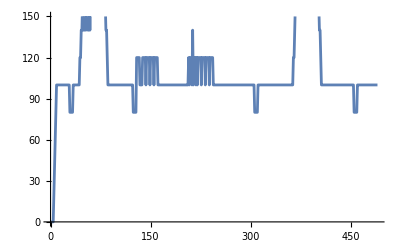

```mathematica
ListLinePlot[table[[16,16,7]]]
```